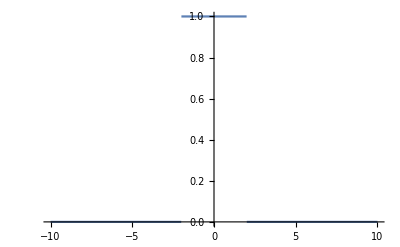

```mathematica
Ft[n_]:=Piecewise[{{0,n<-2 || n>2},{1,2>n>-2}}] 
Plot[Ft[n],{n,-10,10}]

FourierSequenceTransform[Ft[n],n,ω]
```

ⅇ^(-ⅈ ω) (1+ⅇ^(ⅈ ω)+ⅇ^(2 ⅈ ω))

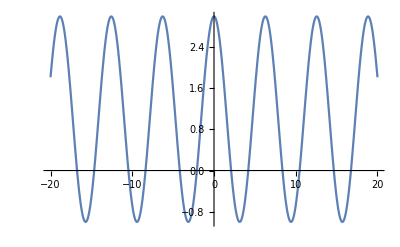

```mathematica
ⅇ^(-ⅈ ω) (1+ⅇ^(ⅈ ω)+ⅇ^(2 ⅈ ω))
Plot[%,{ω,-20,20}]
```